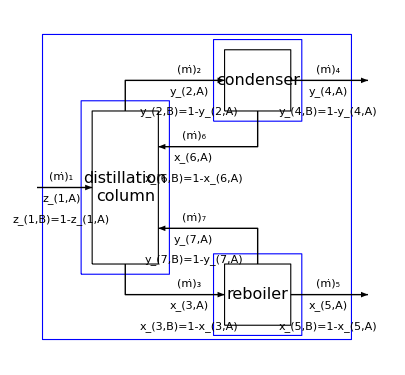

```mathematica
Module[{unit,labels,equipment,streams,variables},
unit[pos_,side_]:={Rectangle[{pos[[1]]-1.5,pos[[2]]-side*1.5},{pos[[1]]+1.5,pos[[2]]+side*1.5}],
Rectangle[{pos[[1]]-2,pos[[2]]-(side*1.5+0.5)},{pos[[1]]+2,pos[[2]]+(side*1.5+0.5)}]};

labels[number_,cmp_,pos_]:={#1,{#2,#3}}&@@(Style[#,15]&/@Flatten@{
Text[Subscript[OverDot@Style["m",Italic],number],{pos[[1]],pos[[2]]+0.55}],
{Text[Subscript[Style[cmp,Italic],Row@{number,",A"}],{pos[[1]],pos[[2]]-0.55}],
Text[Row@{Subscript[Style[cmp,Italic],Row@{number,",B"}],"=1-",Subscript[Style[cmp,Italic],Row@{number,",A"}]},{pos[[1]],pos[[2]]-1.55}]}});

equipment={
Flatten@{"distillation column",unit[{0,0},2.5],Text[Style[Column[{"distillation","column"},Center],16],{0,0}]},
Flatten@{"condenser",unit[{6,5.25},1],Text[Style["condenser",16],{6,5.25}]},
Flatten@{"reboiler",unit[{6,-5.25},1],Text[Style["reboiler",16],{6,-5.25}]},
{"overall",Text@"",Rectangle[{-3.75,-7.45},{10.25,7.5}],Text@""}};

streams={Arrow[{{-4.,0},{-1.5,0}}],Arrow[{{0,3.75},{0,5.25},{4.5,5.25}}],Arrow[{{0,-3.75},{0,-5.25},{4.5,-5.25}}],Arrow[{{7.5,5.25},{11,5.25}}],Arrow[{{7.5,-5.25},{11,-5.25}}],Arrow[{{6,3.75},{6,2},{1.5,2}}],Arrow[{{6,-3.75},{6,-2},{1.5,-2}}]};

variables=(*Style[#,17]&/@*){(*"feed",*)labels[1,"z",{-2.9,0}],(*"vapor",*)labels[2,"y",{2.9,5.25}],(*"liquid",*)labels[3,"x",{2.9,-5.25}],
(*"overhead",*)labels[4,"y",{9.2,5.25}],(*"bottoms",*)labels[5,"x",{9.2,-5.25}],(*"reflux",*)labels[6,"x",{3.1,2}],(*"reboil",*)labels[7,"y",{3.1,-2}]};

Graphics[{
{FaceForm@None,EdgeForm@Thick,equipment[[All,2]],EdgeForm@{Thick,Dashed,Blue},equipment[[All,3]]},equipment[[All,4]],{Thick,streams},variables
},ImageSize->{405,375},AspectRatio->Full,PlotRange->{-7.51,7.51}]
]
```

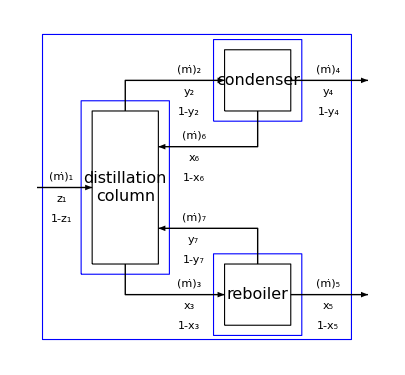

```mathematica
Module[{unit,labels,equipment,streams,variables},
unit[pos_,side_]:={Rectangle[{pos[[1]]-1.5,pos[[2]]-side*1.5},{pos[[1]]+1.5,pos[[2]]+side*1.5}],
Rectangle[{pos[[1]]-2,pos[[2]]-(side*1.5+0.5)},{pos[[1]]+2,pos[[2]]+(side*1.5+0.5)}]};

labels[number_,cmp_,pos_]:={#1,{#2,#3}}&@@(Style[#,17]&/@Flatten@{
Text[Subscript[OverDot@Style["m",Italic],number],{pos[[1]],pos[[2]]+0.55}],
{Text[Subscript[Style[cmp,Italic],number],{pos[[1]],pos[[2]]-0.55}],
Text[Row@{"1-",Subscript[Style[cmp,Italic],number]},{pos[[1]],pos[[2]]-1.55}]}});

equipment={
Flatten@{"distillation column",unit[{0,0},2.5],Text[Style[Column[{"distillation","column"},Center],16],{0,0}]},
Flatten@{"condenser",unit[{6,5.25},1],Text[Style["condenser",16],{6,5.25}]},
Flatten@{"reboiler",unit[{6,-5.25},1],Text[Style["reboiler",16],{6,-5.25}]},
{"overall",Text@"",Rectangle[{-3.75,-7.45},{10.25,7.5}],Text@""}};

streams={Arrow[{{-4.,0},{-1.5,0}}],Arrow[{{0,3.75},{0,5.25},{4.5,5.25}}],Arrow[{{0,-3.75},{0,-5.25},{4.5,-5.25}}],Arrow[{{7.5,5.25},{11,5.25}}],Arrow[{{7.5,-5.25},{11,-5.25}}],Arrow[{{6,3.75},{6,2},{1.5,2}}],Arrow[{{6,-3.75},{6,-2},{1.5,-2}}]};

variables=(*Style[#,17]&/@*){(*"feed",*)labels[1,"z",{-2.9,0}],(*"vapor",*)labels[2,"y",{2.9,5.25}],(*"liquid",*)labels[3,"x",{2.9,-5.25}],
(*"overhead",*)labels[4,"y",{9.2,5.25}],(*"bottoms",*)labels[5,"x",{9.2,-5.25}],(*"reflux",*)labels[6,"x",{3.1,2}],(*"reboil",*)labels[7,"y",{3.1,-2}]};

Graphics[{
{FaceForm@None,EdgeForm@Thick,equipment[[All,2]],EdgeForm@{Thick,Dashed,Blue},equipment[[All,3]]},equipment[[All,4]],{Thick,streams},variables
},ImageSize->{405,375},AspectRatio->Full,PlotRange->{-7.51,7.51}]
]
```

```mathematica
Manipulate[
Module[{unit,labels,equipment,streams,variables},
unit[pos_,side_]:={Rectangle[{pos[[1]]-1.5,pos[[2]]-side*1.5},{pos[[1]]+1.5,pos[[2]]+side*1.5}],
Rectangle[{pos[[1]]-1.9,pos[[2]]-(side*1.5+0.4)},{pos[[1]]+1.9,pos[[2]]+(side*1.5+0.4)}]};

labels[number_,cmp_,pos_]:={#1,{#2,#3}}&@@(Style[#,16]&/@Flatten@{
Text[Subscript[OverDot@Style["m",Italic],number],{pos[[1]],pos[[2]]+0.55}],
{Text[Subscript[Style[cmp,Italic],Row@{number,",A"}],{pos[[1]],pos[[2]]-0.55}],
Text[Row@{"1-",Subscript[Style[cmp,Italic],Row@{number,",A"}]},{pos[[1]],pos[[2]]-1.55}]}});

equipment={
Flatten@{"distillation column",unit[{0,0},2.5],Text[Style[Column[{"distillation","column"},Center],16],{0,0}]},
Flatten@{"condenser",unit[{6,5.25},1],Text[Style["condenser",16],{6,5.25}]},
Flatten@{"reboiler",unit[{6,-5.25},1],Text[Style["reboiler",16],{6,-5.25}]},
{"overall",Text@"",Rectangle[{-3.9,-7.45},{10.25,7.5}],Text@""}};

streams={Arrow[{{-4.2,0},{-1.5,0}}],Arrow[{{0,3.75},{0,5.25},{4.5,5.25}}],Arrow[{{0,-3.75},{0,-5.25},{4.5,-5.25}}],Arrow[{{7.5,5.25},{11,5.25}}],Arrow[{{7.5,-5.25},{11,-5.25}}],Arrow[{{6,3.75},{6,2},{1.5,2}}],Arrow[{{6,-3.75},{6,-2},{1.5,-2}}]};

variables={
If[npr==1,
ReplacePart[labels[1,"z",{-2.9,0}],{2,2}->Text[Style[Row@{Subscript[Style["z",Italic],"1,B"],"=1-",Subscript[Style["z",Italic],"1,A"]},16,Background->White],{-3.1,-1.55}]],
ReplacePart[labels[1,"z",{-2.9,0}],{2,2}->Text[Style[Column[{Row@{Subscript[Style["z",Italic],"1,B"],"="},Row@{"1-",Subscript[Style["z",Italic],"1,A"]}},Center],16],{-2.9,-2.05}]]
],
labels[2,"y",{3,5.25}],labels[3,"x",{2.9,-5.25}],
labels[4,"y",{9.2,5.25}],labels[5,"x",{9.2,-5.25}],labels[6,"x",{3.1,2}],labels[7,"y",{3,-2}]};

Graphics[{
{FaceForm@None,EdgeForm@Thick,equipment[[All,2]],EdgeForm@{Thick,Dashed,Blue},equipment[[select,3]]},equipment[[All,4]],{Thick,streams},(*Style[#,Blue,Bold]&/@*)variables
},ImageSize->{405,375},AspectRatio->Full,PlotRange->{-7.51,7.51}]
],
Control[{{npr,1},{1,2},Setter}],
Control[{{select,2,"balance"},{1->" column ",2->" condenser ",3->" reboiler ",4->" overall "},Setter}]
]
```